## Use the Effect Size to determine differences between data:

### Inputs:

```mathematica
tempdata = a00;
Dimensions/@a00
mediansData  = Median/@a00
```

{{72},{31},{106}}

{202.969,126.336,166.202}

#### Colors and settings:

```mathematica
color1 = RGBColor[0.12, 0.77, 0.61];
color2 = RGBColor[0.66, 0.06, 0.78];
color3 = RGBColor[0.9500000000000001, Rational[2, 3], 0];
```

```mathematica
(*for voilin plots*)times= {.75,1.75,2.75};
(*times= {1,2,3};*)
```

### Functions:

#### Significance calculator for effect size:

Input the confidence intervals, list of {#1, #2} per dataset, and the ONE median you want to use as a comparison (#, for example, the TA median which I think is sig diff from my two controls)

```mathematica
MyEffectSizeSignaficanceTester[confIntsEffectSize_, effectSizeMedians_] := 
Table[ 
If[ confIntsEffectSize[[i,1]]< effectSizeMedians< confIntsEffectSize[[i,2]],  "Not significantly different" ,"Significantly different at 0.05 confidence interval"]
,{i,1,Length@confIntsEffectSize}]//TableForm
```

### Bootstrapping medians and calculating Effect Size:

#### Setting bootstrapping Parameters:

```mathematica
sampleSize = Length/@tempdata  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 10000;  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

{72,31,106}

#### Bootstrapping for Nuc Accum intensity data:

RANDOM CHOICE : pick > once  
RANDOM SAMPLE : pick = once

```mathematica
bootstrapData= Table[  Table[Table[RandomChoice[tempdata[[i]]],sampleSize[[i]]],repetitions ] , {i,1,Length@tempdata,1}];
Dimensions/@bootstrapData
```

{{10000,72},{10000,31},{10000,106}}

Using the MEDIAN, not the MEAN, of #repetitions of bootstrap data

```mathematica
mediansBS0 = N/@Table[Table[Median[bootstrapData[[i,j]]],{j,1,Length@bootstrapData[[i]],1}],{i,1,Length@bootstrapData,1}];
mediansBS = Sort/@mediansBS0; 
(*stdevsBS = N/@StandardDeviation/@mediansBS 
errorBS =ErrorBar/@stdevsBS; *)
```

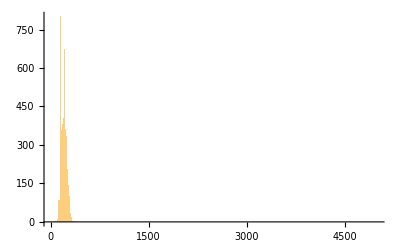
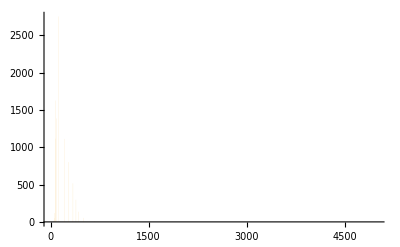
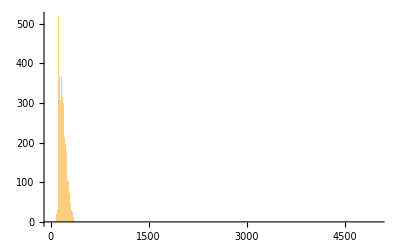

```mathematica
Histogram[#, 250, PlotRange->{{0,5000},{All,All}}]&/@mediansBS
```

Find the 5%  -  95% confidence interval (CI)

```mathematica
confInts = mediansBS[[All, (repetitions*.025) ;;All;;(repetitions*.95) ]];
confIntsThreaded = Table[  {Thread[ {times, confInts[[All,1]]}], Thread[ {times, confInts[[All,2]]}]} [[All,i]], {i,1,3}]; 
confInts//TableForm
```

131.736 | 292.645
70.232 | 388.766
116.259 | 308.934

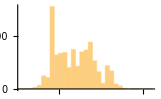

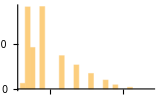

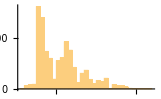

```mathematica
Histogram[  mediansBS[[1]]-mediansData[[3]]  ]
Histogram[  mediansBS[[2]]-mediansData[[3]]  ]
Histogram[  mediansBS[[3]]-mediansData[[3]]  ]
```

#### Calculate Effect Size

```mathematica
effectSize = Table[  mediansBS[[i]]-mediansData[[3]]   , {i, 1,3}];
effectSizeMedians = Table[  mediansData[[i]]-mediansData[[3]]   , {i, 1,3}]
```

{36.7675,-39.866,0.}

```mathematica
confIntsEffectSize = effectSize[[All, (repetitions*.025) ;;All;;(repetitions*.95) ]];
confIntsEffectSize//TableForm
```

-34.466 | 126.443
-95.97 | 222.564
-49.943 | 142.732

```mathematica
confIntsThreaded = Table[  {Thread[ {times, confIntsEffectSize[[All,1]]}], Thread[ {times, confIntsEffectSize[[All,2]]}]} [[All,i]], {i,1,3}];
```

### Visualize the Effect Size and compare multiple data sets

Effect size determines if two datasets are different or the same. 
*Comparisons are ALWAYS made to the 3rd dataset, TA

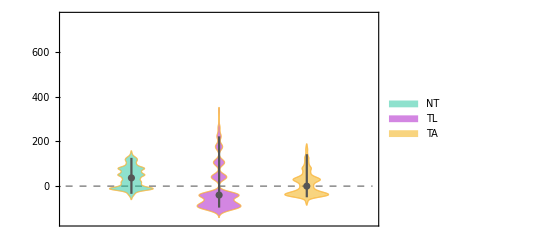

NT compared to TA,   TL compared to TA,   TA compared to TA:

Not significantly differnet
Not significantly differnet
Not significantly differnet

```mathematica
Show[  
DistributionChart[ {effectSize[[1]], effectSize[[2]], effectSize[[3]]} , ChartStyle->  {Opacity[0, color1] , Opacity[0., color2] ,  Opacity[0., color3] } ] , 

Plot[0,{x,0,3.5}, PlotStyle->{Thickness[.0025], Opacity[1,Gray], Dashed}],

DistributionChart[ {effectSize[[1]], effectSize[[2]], effectSize[[3]]} , ChartStyle->  {Opacity[0.5, color1] , Opacity[0.5, color2] ,  Opacity[0.5, color3] } , ChartLegends-> {"NT", "TL", "TA"}]     ,
ListLinePlot[ confIntsThreaded, PlotStyle->Darker[Gray]]  , 
ListPlot  [ Thread[ {times,effectSizeMedians}] , PlotStyle->Darker[Gray ]] 
, PlotRange-> All , AxesOrigin-> {0.5,0} 
]
"NT compared to TA,   TL compared to TA,   TA compared to TA:  "
MyEffectSizeSignaficanceTester[confIntsEffectSize, effectSizeMedians[[3]]]
```